```mathematica
(* inputs *)
ωXi = 1/ΔXi^2;
ωYi = 1/ΔYi^2;
ri=todo;
```

```mathematica
bList = {}

yorkFitRaw[Xi_, Yi_, ωXi_, ωYi_, ri_]:= Module[
{iterateParametersFor, fit, b0, 
αi, Wi, Wsum, Xmean, Ymean, Ui, Vi, βi, a,b,xi, xmean,ui, σbSq,σaSq, 
n = 1},

(* Step 1 *)
fit = LinearModelFit[Transpose[{Xi, Yi}], x, x, Weights-> ωYi];
b0 = fit["BestFitParameters"]⟦2⟧;

(* Step 2 *)
(* done at input time*)

iterateParametersFor[b_]:=Module[{bNew},
(* Step 3 *)
αi=Sqrt[ωXi*ωYi];
Wi=(ωXi*ωYi)/(ωXi+b^2  ωYi-2b  ri  αi);

(* Step 4 *)
Wsum = Total[Wi];
Xmean = Total[Wi* Xi]/Wsum ;
Ymean = Total[Wi* Yi]/Wsum ;

Ui = Xi - Xmean;
Vi = Yi - Ymean;

βi= Wi * (Ui / ωYi  + b Vi / ωXi - (b Ui - Vi) ri / αi );
(*βmean = Total[Wi* βi]/Wsum;*)

(* Step 5 *)

bNew = Total[Wi * βi * Vi] / Total[Wi*βi*Ui];
bNew
];

(* Step 6 *)

While[ n< 10000,
b = iterateParametersFor[b0];
If[Abs[b-b0]< 10^-12,Break[]];
(*bList = Append[bList, Abs[b-b0]];*)
b0 = b;
n++
];
If[n ≥ 10000-1 , Print["Warning: York fit failed to converge in ", n," iterations"]];

(* Step 7 *)
a = Ymean - b * Xmean;

(* Step 8 *)
xi = Xmean - βi;
(*yi = Ymean - b* βi;*)

(* Step 9 *) 
xmean = Total[Wi* xi]/Wsum ;
(*ymean = Total[Wi* yi]/Wsum ;*)
ui = xi - xmean;
(*vi = yi - ymean;*)
(*S= Total[Wi (Yi -b Xi - a)^2];*)

(* Step 10 *)
σbSq = 1/Total[Wi ui^2];
σaSq = 1/Wsum  + xmean^2 σbSq;

(* return all*)
Return[<|"a" -> a, "b" -> b, "σa" -> Sqrt[σaSq], "σb" -> Sqrt[σbSq]|> ];
]
```

{}

#### Original Code

```mathematica
(*original function from stackexchange*)ortlinfit[data_?MatrixQ,errs_?MatrixQ]:=Module[{n=Length[data],c,ct,dk,dm,k,m,p,s,st,ul,vl,w,wt,xm,ym},(*yes,I know I could have used FindFit[] for this...*){ct,st,k}=Flatten[MapAt[Normalize[{1,#}]&,NArgMin[Norm[Function[{x,y},y-m x-k]@@@data],{m,k}],1]];
(*find orthogonal regression coefficients*){c,s,p}=FindArgMin[{Total[(data.{-s,c}-p)^2/((errs^2).{s^2,c^2})],c^2+s^2==1},{{c,ct},{s,st},{p,k/ct}}];
(*slope and intercept*){m,k}={s,p}/c;
wt=1/errs^2;w=(Times@@@wt)/(wt.{1,m^2});
{xm,ym}=w.data/Total[w];
ul=data[[All,1]]-xm;vl=data[[All,2]]-ym;
(*uncertainties in slope and intercept*)dm=w.(m ul-vl)^2/w.ul^2/(n-2);
dk=dm (w.data[[All,1]]^2/Total[w]);
{Function[x,Evaluate[{m,k}.{x,1}]],Sqrt[{dm,dk}]}]/;Dimensions[data]===Dimensions[errs]
```

#### Testing

```mathematica
(*testing cases*)
data={{0,5.9},{0.9,5.4},{1.8,4.4},{2.6,4.6},{3.3,3.5},{4.4,3.7},{5.2,2.8},{6.1,2.8},{6.5,2.4},{7.4,1.5}};
errs={{1000.,1.},{1000.,1.8},{500.,4.},{800.,8.},{200.,20.},{80.,20.},{60.,70.},{20.,70.},{1.8,100.},{1,500.}}//Sqrt[1/#]&;
{lin,{sm,sk}}=ortlinfit[data,errs]
```

{Function[x$,5.47991-0.480533 x$],{0.0710065,0.361871}}

```mathematica
fit = yorkFitRaw[
data⟦All,1⟧, 
data⟦All,2⟧, 
errs⟦All,1⟧^-2, 
errs⟦All,2⟧^-2, 
ConstantArray[0.0, Length[data]]
]
```

<|a→5.47991,b→-0.480533,σa→0.29628,σb→0.057985|>

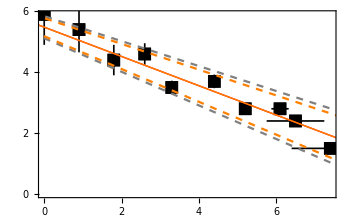

```mathematica
lin2[x_]:= fit["a"] + x *fit["b"];
sm2 = fit["σb"];
sk2 = fit["σa"];
Show[
OListPlot[data, ErrorBars -> errs],
(*Plot[ fit["a"] + x *fit["b"], {x,Min[data⟦All,1⟧], Max[data⟦All,1⟧]}],*)
Plot[{lin[x],lin[x]-sm x-sk,lin[x]+sm x+sk},{x,-1,9},PlotStyle->{Directive[Thick,Red],Directive[Dashed,Gray],Directive[Dashed,Gray]}],
Plot[{lin2[x],lin2[x]-sm2 x-sk2,lin2[x]+sm2 x+sk2},{x,-1,9},PlotStyle->{Directive[Thick,Orange],Directive[Dashed,Orange],Directive[Dashed,Orange]}]

]
```

```mathematica
<<YorkFit`
```

```mathematica
YorkFit[data, "Errors" -> errs, IncludeConstantBasis->False]
```

<|a→5.5004×10^-99,b→0.605297,σa→1.16892×10^-50,σb→0.0187114,fit→Function[x$,5.5004×10^-99+0.605297 x$],fitFunction→Function[x,a+b x],BestFitParameters→{5.5004×10^-99,0.605297},Errors→{1.16892×10^-50,0.0187114}|>

```mathematica
?YorkFit
```

YorkFit[{{x,y},...}, "Errors"-> err] York linear regression fit:
  http://aapt.scitation.org/doi/pdf/10.1119/1.1632486
  
  "Errors" can be supplied with:
    Automatic - assumes 5% error variation in X and Y
    None - no errors in x and y
    p_NumberQ - assumes the erros are p fraction of the data
    {pX_NumberQ, pY_NumberQ} - assumes the erros are {pX,pY} fraction of the data
    {errY1,errY2,...} - errors only in Y
    {{errX1,errY1},...} - errors in x and y
  
  Weights -> None
    Allows to manually specify weight matrix

  "ErrorCorrelations" -> None
    Correlations between X and Y errors

  IncludeConstantBasis -> True
    if False, this leads to fit y=b*x
    achieved by adding {0,0} point with very high weights 

  Output: <|"fit" -> best fit, "a" -> offset, "b" -> slope, "σa" -> error of offset, 
    "σb" -> error of slope |>